1 PUNTO DE EQUILIBRIO

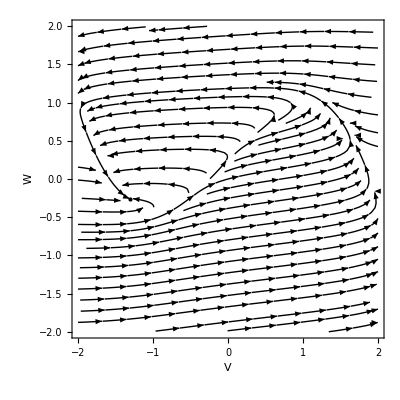

```mathematica
ϕ = 0.08; a = 1; b = 1.2; T = 0.3;
f[{V_, W_}] := {V - V^3/3 - W + T, ϕ (V + a - b W)};

campo = StreamPlot[{f[{V, W}][[1]], f[{V, W}][[2]]}, {V, -2, 2}, {W, -2, 2}, StreamColorFunction -> None, StreamStyle -> Directive[Black]];

punto = Graphics[{Black, PointSize[Large], Point[{-1.3115, -0.2596}]}];

Show[campo, punto, Frame -> True, FrameLabel -> {Style[ToExpression["V", TeXForm, HoldForm]], Style[ToExpression["W", TeXForm, HoldForm]]}]
```

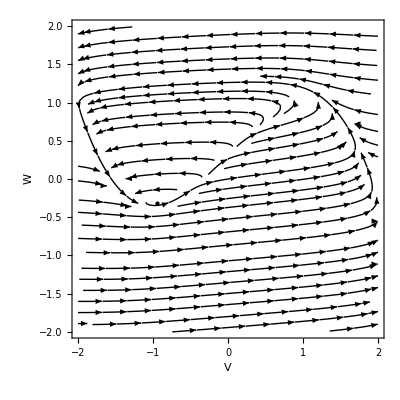

```mathematica
ϕ = 0.08; a = 0.7; b = 0.8; T = 0.35;
f[{V_, W_}] := {V - V^3/3 - W + T, ϕ (V + a - b W)};

campo = StreamPlot[{f[{V, W}][[1]], f[{V, W}][[2]]}, {V, -2, 2}, {W, -2, 2}, StreamColorFunction -> None, StreamStyle -> Directive[Black]];

punto = Graphics[{Black, PointSize[Large], Point[{-0.9515, -0.3143}]}];

Show[campo, punto, Frame -> True, FrameLabel -> {Style[ToExpression["V", TeXForm, HoldForm]], Style[ToExpression["W", TeXForm, HoldForm]]}]
```

```mathematica
ϕ = 0.08; a = 1; b = 1.5; T = 0.85;
f[{V_, W_}] := {V - V^3/3 - W + T, ϕ (V + a - b W)};

campo = StreamPlot[{f[{V, W}][[1]], f[{V, W}][[2]]}, {V, -2, 2}, {W, -2, 2}, StreamColorFunction -> None, StreamStyle -> Directive[Black]];

punto = Graphics[{Black, PointSize[Large], Point[{1.2066, 1.4711}]}];

Show[flujo, punto, Frame -> True, FrameLabel -> {Style[ToExpression["V", TeXForm, HoldForm]], Style[ToExpression["W", TeXForm, HoldForm]]}]
```

Show::gcomb: Could not combine the graphics objects in Show[flujo,,Frame→True,FrameLabel→{V,W}].

Show[flujo,-Graphics-,Frame→True,FrameLabel→{V,W}]

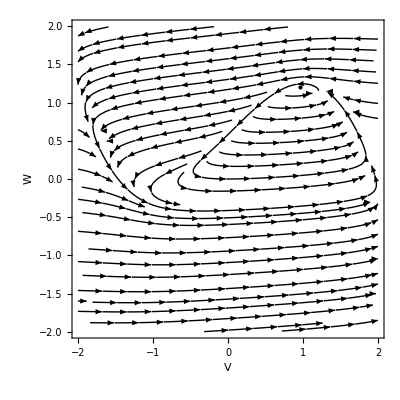

```mathematica
ϕ = 0.1; a = 0; b = 0.8; T = 3249/6085;
f[{V_, W_}] := {V - V^3/3 - W + T, ϕ (V + a - b W)};

campo = StreamPlot[{f[{V, W}][[1]], f[{V, W}][[2]]}, {V, -2, 2}, {W, -2, 2}, StreamColorFunction -> None, StreamStyle -> Directive[Black]];

punto = Graphics[{Black, PointSize[Large], Point[{0.9592, 1.1990}]}];

Show[campo, punto, Frame -> True, FrameLabel -> {Style[ToExpression["V", TeXForm, HoldForm]], Style[ToExpression["W", TeXForm, HoldForm]]}]
```

2 PUNTOS DE EQUILIBRIO

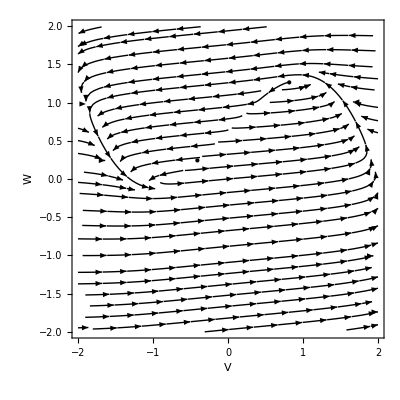

```mathematica
ϕ = 0.08; a = 0.7; b = 1.2; T = 1170/1861;
f[{V_, W_}] := {V - V^3/3 - W + T, ϕ (V + a - b W)};

campo = StreamPlot[{f[{V, W}][[1]], f[{V, W}][[2]]}, {V, -2, 2}, {W, -2, 2}, StreamColorFunction -> None, StreamStyle -> Directive[Black]];

punto = Graphics[{
  Black, PointSize[Large], 
  Point[{-0.4082, 0.2431}], 
  Point[{0.8165, 1.2637}]
  }];

Show[campo, punto, Frame -> True, FrameLabel -> {Style[ToExpression["V", TeXForm, HoldForm]], Style[ToExpression["W", TeXForm, HoldForm]]}]
```

3 PUNTOS DE EQUILIBRIO

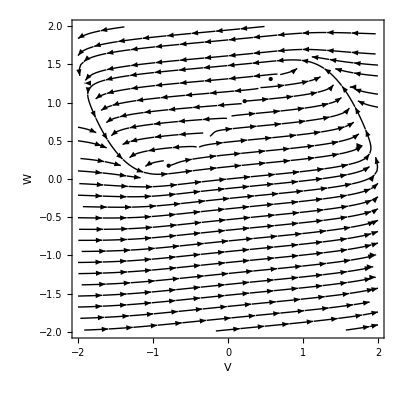

```mathematica
ϕ = 0.08; a = 1; b = 1.2; T = 0.8;
f[{V_, W_}] := {V - V^3/3 - W + T, ϕ (V + a - b W)};

campo = StreamPlot[{f[{V, W}][[1]], f[{V, W}][[2]]}, {V, -2, 2}, {W, -2, 2}, StreamColorFunction -> None, StreamStyle -> Directive[Black]];

punto = Graphics[{
  Black, PointSize[Large], 
  Point[{0.2218, 1.0182}], 
  Point[{0.5696, 1.3080}], 
  Point[{-0.7914, 0.1738}]
  }];

Show[campo, punto, Frame -> True, FrameLabel -> {Style[ToExpression["V", TeXForm, HoldForm]], Style[ToExpression["W", TeXForm, HoldForm]]}]
```